```mathematica
Clear["Global`*"]
```

```mathematica
x = 0.1;
listpoints = {};
j=1;
For[μ = 3.8, μ<3.830,μ=μ+0.00002,
For[i=1,i<500,i++,
x = μ x(1-x)
];
AppendTo[listpoints,{μ}];
For[i=1,i<20000,i++,
x =μ x(1-x);
AppendTo[listpoints⟦j⟧,x];
];
j++;
]

listpointsx = listpoints⟦All,2 ;;⟧;
```

```mathematica
listpointsp = {};
For[k=0, k<Length[listpoints],k++;
For[n=1, n<Length[listpoints⟦k⟧],n++;
AppendTo[listpointsp,{listpoints⟦k,1⟧,listpoints⟦k,n⟧}]]]
```

```mathematica
listpoints⟦1⟧
```

{3.8,0.85387,0.474149,0.947461,0.18916,0.582839,0.923923,0.267098,0.743875,0.723995,0.75934,0.694422,0.80636,0.593345,0.91689,19970,0.777113,0.658193,0.854905,0.471361,0.946883,0.191122,0.587459,0.920933,0.276697,0.760516,0.692099,0.809772,0.585358,0.922313,0.272276}
 |  |  |  |

```mathematica
tempfile = FileNameJoin[{$TemporaryDirectory, "test.wl"}]
```

/private/var/folders/j4/2c2cfr0s369f2xwnypbvrl6h0000gn/T/test.wl

```mathematica
Save[tempfile, {listpoints,listpointsx}]
```

```mathematica
Get[tempfile]
```

Get::stream: tempfile is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

$Failed

```mathematica
σ =  0.1;
s = 0.1;
t = 0.1;
listμpeakTotal = {};
For[ i=0, i< Length[listpointsx],i++;
HLlocal = HistogramList[listpointsx⟦i⟧,{0,1,5 10^-4}, "PDF"];
peaksl  = FindPeaks[HLlocal⟦2⟧, σ, s, t];
indexesl = Round[peaksl[[All,1]]];
AppendTo[listμpeakTotal,{}];
AppendTo[listμpeakTotal⟦i⟧,listpoints⟦i,1⟧];
For[j=0,j <Length[indexesl], j++;
AppendTo[listμpeakTotal⟦i⟧,HLlocal⟦1,indexesl⟦j⟧⟧]]]
listμpeakTotalp = {};
For[k=0, k<Length[listμpeakTotal],k++;
For[n=1, n<Length[listμpeakTotal⟦k⟧],n++;
AppendTo[listμpeakTotalp,{listμpeakTotal⟦k,1⟧,listμpeakTotal⟦k,n⟧}]]]

ListPlot[listμpeakTotalp, GridLines->Automatic]
```

$Aborted

-Graphics-

```mathematica
lengthcurves = {};

curva1Astep = Select[listμpeakTotalp, #⟦1⟧ < 3.820 &];
curva1Astep2 = Select[curva1Astep, 0.1 < #⟦2⟧ < 0.18 &];
AppendTo[lengthcurves,Length[curva1Astep2 ]];
curva1A = DeleteDuplicates[curva1Astep2, #1⟦1⟧ == #2⟦1⟧ &];
coef1A = FindFit[curva1A, a xv^2 + b xv + c, {a,b, c},xv];

curva1Bstep = Select[listμpeakTotalp, #⟦1⟧ < 3.820 &];
curva1Bstep2 = Select[curva1Bstep, 0.18 < #⟦2⟧ < 0.23 &];
AppendTo[lengthcurves,Length[curva1Bstep2 ]];
curva1B = DeleteDuplicates[curva1Bstep2, #1⟦1⟧ == #2⟦1⟧ &];
coef1B = FindFit[curva1B, a xv^2 + b xv + c, {a,b,c},xv];

curva1Cstep = Select[listμpeakTotalp, #⟦1⟧ < 3.815 &];
curva1Cstep2 = Select[curva1Cstep, 0.25 < #⟦2⟧ < 0.5 &];
AppendTo[lengthcurves,Length[curva1Cstep2 ]];
curva1C = DeleteDuplicates[curva1Cstep2, #1⟦1⟧ == #2⟦1⟧ &];
coef1C = FindFit[curva1C, a xv^2 + b xv + c, {a,b, c},xv];

curva2Astep = Select[listμpeakTotalp, #⟦1⟧ < 3.817 &];
curva2Astep2 = Select[curva2Astep, 0.52 < #⟦2⟧ < 0.56 &];
AppendTo[lengthcurves,Length[curva2Astep2 ]];
curva2A = DeleteDuplicates[curva2Astep2, #1⟦1⟧ == #2⟦1⟧ &];
coef2A = FindFit[curva2A, a xv^2 + b xv + c, {a,b, c},xv];

curva2Bstep = Select[listμpeakTotalp, #⟦1⟧ < 3.820 &];
curva2Bstep2 = Select[curva2Bstep, 0.562 < #⟦2⟧ < 0.7 &];
AppendTo[lengthcurves,Length[curva2Bstep2 ]];
curva2B = DeleteDuplicates[curva2Bstep2, #1⟦1⟧ == #2⟦1⟧ &];
coef2B = FindFit[curva2B, a xv^2 + b xv + c, {a,b, c},xv];

curva3Astep = Select[listμpeakTotalp, #⟦1⟧ < 3.820 &];
curva3Astep2 = Select[curva3Astep, 0.80 < #⟦2⟧ < 0.93 &];
AppendTo[lengthcurves,Length[curva3Astep2 ]];
curva3A = DeleteDuplicates[curva3Astep2, #1⟦1⟧ == #2⟦1⟧ &];
coef3A = FindFit[curva3A,a xv^2 + b xv + c, {a,b,c},xv];

curva3Bstep = Select[listμpeakTotalp, #⟦1⟧ < 3.815 &];
curva3Bstep2 = Select[curva3Bstep, 0.93 < #⟦2⟧ < 0.95 &];
AppendTo[lengthcurves,Length[curva3Bstep2 ]];
curva3B = DeleteDuplicates[curva3Bstep2, #1⟦1⟧ == #2⟦1⟧ &];
coef3B = FindFit[curva3B, a xv + b , {a,b},xv];

curva3Cstep = Select[listμpeakTotalp, #⟦1⟧ < 3.815 &];
curva3Cstep2 = Select[curva3Cstep, 0.949< #⟦2⟧ < 0.96 &];
AppendTo[lengthcurves,Length[curva3Cstep2 ]];
curva3C= DeleteDuplicates[curva3Cstep2, #1⟦1⟧ == #2⟦1⟧ &];
coef3C = FindFit[curva3C, a xv^2 + b xv + c, {a,b, c},xv];
```

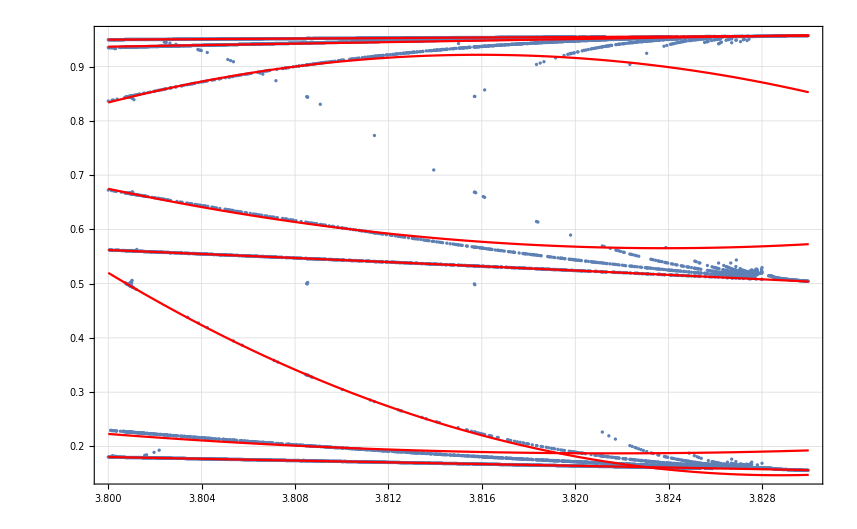

```mathematica
Show[ListPlot[listμpeakTotalp],
Plot[ a xv^2 + b xv + c/.coef1A, {xv, 3.800, 3.830}, PlotStyle->Red],
Plot[  a xv^2 + b xv + c/.coef1B, {xv, 3.800, 3.830}, PlotStyle->Red],
Plot[ a xv^2 + b xv + c/.coef1C, {xv, 3.800, 3.830}, PlotStyle->Red],
Plot[ a xv^2 + b xv + c/.coef2A, {xv, 3.800, 3.830}, PlotStyle->Red],
Plot[ a xv^2 + b xv + c/.coef2B, {xv, 3.800, 3.830}, PlotStyle->Red],
Plot[  a xv^2 + b xv + c/.coef3A, {xv, 3.800, 3.830}, PlotStyle->Red],
Plot[ a xv + b/.coef3B, {xv, 3.800, 3.830}, PlotStyle->Red],
Plot[ a xv^2 + b xv + c/.coef3C, {xv, 3.800, 3.830}, PlotStyle->Red],
 Frame-> True, GridLines-> Automatic, PlotRange->  Automatic]
```

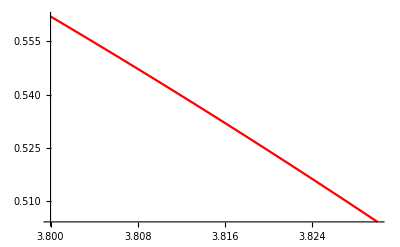

```mathematica
Plot[ a xv^2 + b xv + c/.coef, {xv, 3.800, 3.830}, PlotStyle->Red]
```

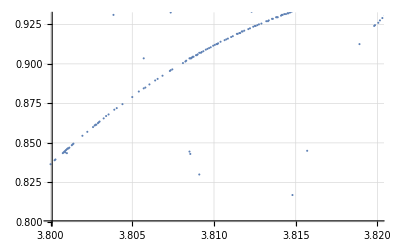

```mathematica
ListPlot[listμpeakTotalp, GridLines -> Automatic, PlotRange -> {{3.800, 3.820}, {0.80, 0.93}}]
```

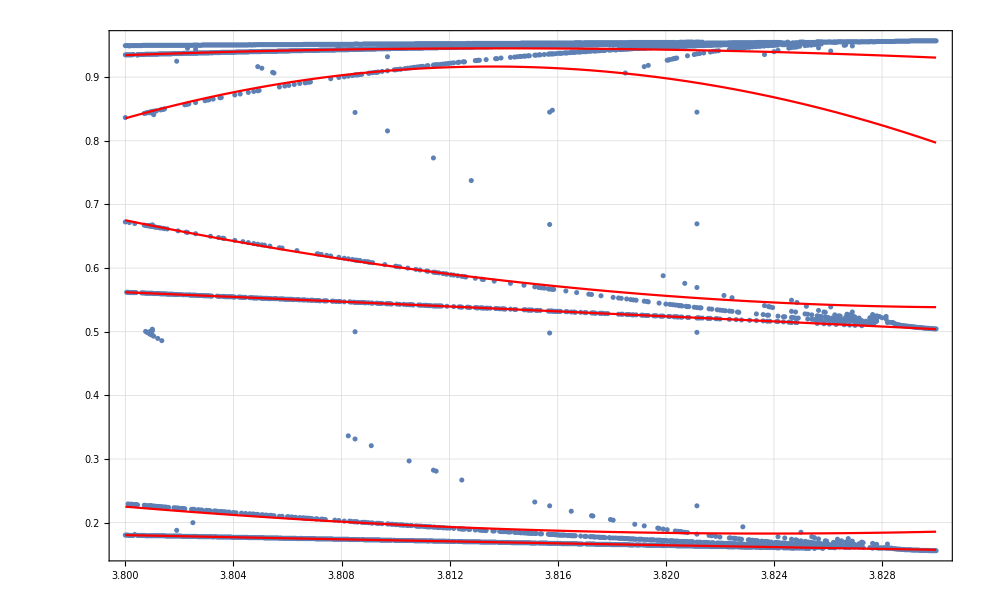
Fits encontrados para curvas 1A, 1B, 2A e 2B utilizando parâmetros:
- de thelistpoints i = 20.000, passo =  0.00005
- de HistogramList bin = 5 x 10^-4
- de FindPeaks σ = 1.3,  s = 0.9,  t = 3.0:
coef1A = {a → 2.75306, b → -21.7759 , c → 43.1745}
coef1B = {a → 74.9319, b → -573.041, c → 1095.77}
coef2A = {a → -3.85675, b → 27.4968, c → -48.2345}
coef2B = {a → 138.465, b → -1061.04, c → 2033.18}
coef3A = {a → -442.554, b → 3375.41, c → -6435.25}
coef3B = {a → -55.819, b → 425.769, c → -810.963}
coef3C = {a→-0.161814,b→1.4821,c→-2.3458}

Linear Versions: 
coef1B = {a→-1.27532,b→5.06031}
coef3B = {a→0.624908,b→-1.43848}


- de thelistpoints i = 10.000, passo =  0.0001
- de HistogramList bin = 5 x 10^-4
- de FindPeaks σ = 1.2,  s = 0.8,  t = 3.0:
coef1C = {a→924.499,b→-7057.04,c→13467.5}


-Graphics-

```mathematica
weighted[xv_] =(f1A[xv] lengthcurves⟦1⟧+f1B[xv]  lengthcurves⟦2⟧+f1C[xv] lengthcurves⟦3⟧+f2A[xv]lengthcurves⟦4⟧+f2B[xv]lengthcurves⟦5⟧+f3A[xv]lengthcurves⟦6⟧+f3B[xv]lengthcurves⟦7⟧+f3C[xv]lengthcurves⟦8⟧)/Total[lengthcurves];
```

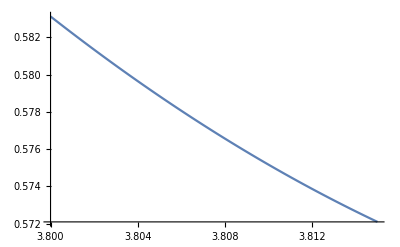

```mathematica
Plot[weighted[xv], {xv,3.800,3.815}]
```

```mathematica
Total[lengthcurves]
```

1698

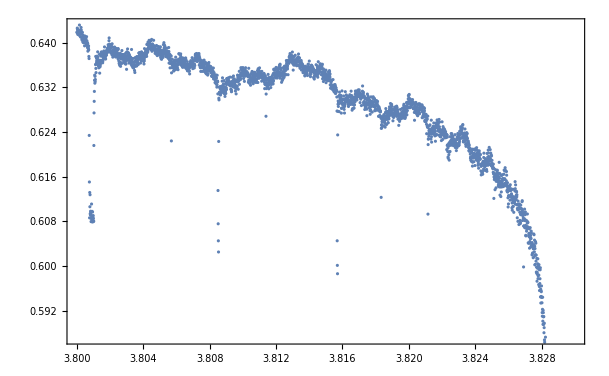
```mathematica
media = -Graphics- ;
```

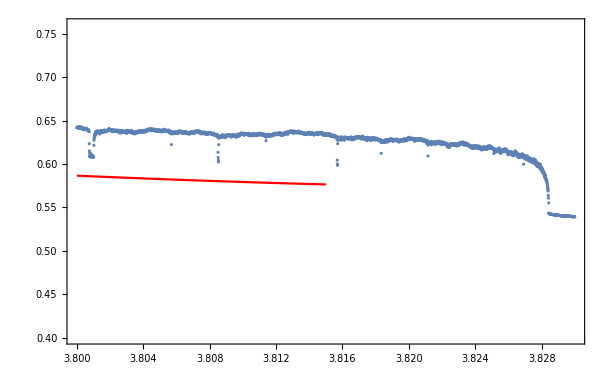

```mathematica
Show[media,Plot[weighted[xv], {xv,3.800,3.815},  PlotStyle->Red], PlotRange-> {0.40,0.76}]
```

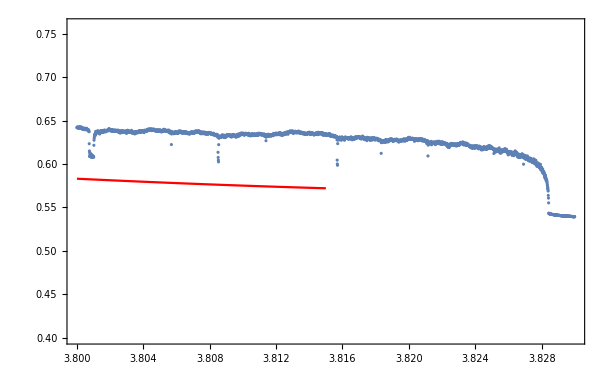

```mathematica
Show[media,Plot[weighted[xv], {xv,3.800,3.815},  PlotStyle->Red], PlotRange-> {0.40,0.76}]
```